## Load Radia

```mathematica
<<Radia`
RadPlot3DOptions[];
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

## Set Directory

```mathematica
SetDirectory["C:\\Users\\luana.vilela\\Desktop"];
```

## Functions

### CreateMagnetModel

```mathematica
CreateMagnetModel[current_] := Module[
{magnet, bobs, bobi, raioin, raioex, espbob, hbobs, hbobi, nespiras, curdensity, seg },

(* Corrente = 1 A *)
(* No de espiras por bobina = 176 *)
(* fio 21  *)
(* raio interno = 10 mm *)
(* raio externo = 19.75 mm*)
(* espessura da bobina = 10.5 mm *)
(* distância entre os centros das bobinas = 19.25 mm *)
(* entre faces 21.8 *)

raioin=10;
raioex=19.75;
espbob=10.5;
hbobs=19.25;
hbobi=19.25;
nespiras = 176;
curdensity=current*nespiras/((raioex-raioin)*espbob);
seg = 100;

bobs=radObjArcCur[{0,0,hbobs},{raioin,raioex},{0,2*Pi},espbob,seg,curdensity];
bobi=radObjArcCur[{0,0,-hbobi},{raioin,raioex},{0,2*Pi},espbob,seg,curdensity];

magnet=radObjCnt[{}]; 
radObjAddToCnt[magnet,{bobs,bobi}]; 

magnet = radTrfOrnt[magnet, radTrfRot[{0,0,0},{1,0,0},π/2]];

Return[magnet];
];
```

### FieldIntegralsMap

```mathematica
FieldIntegralsMap[fieldmapname_, magnet_,xrange_, yrange_, zrange_, nx_, ny_, nz_ ] := Module[
{fieldmap, hmin, hmax, vmin, vmax, nh, nv, hstep, vstep,h, v,   i, j, k,field, line, IBx, IBy, IBz, IIBx, IIBy, IIBz},

fieldmap=OpenWrite[fieldmapname];

hmin =xrange[[1]];
hmax =xrange[[2]];
nh = nx;

vmin =yrange[[1]];
vmax =yrange[[2]];
nv = ny;

If [(hmin ≠ hmax),hstep = (hmax-hmin)/(nh-1), hstep=0 ];
If [(vmin ≠ vmax),vstep = (vmax-vmin)/(nv-1), vstep=0 ];

WriteString[fieldmap, "X[mm]"<> "\t"<> "Y[mm]"<> "\t"<> "IBx[G.cm]"<> "\t"<> "IBy[G.cm]"<> "\t"<> "IBz[G.cm]" <>"\n"];
WriteString[fieldmap,"------------------------------------------------------------------------------------------------------------------------------------------------------------------\n"];
For[j=1,j≤nv,j++,
For[i=1,i≤nh,i++,
h = hmin+(i-1)*hstep;
v = vmin+(j-1)*vstep;
{IBx, IIBx} = FieldIntegrals[magnet, "Bx", h, v, zrange, nz, 1];
{IBy, IIBy} = FieldIntegrals[magnet, "By",h, v, zrange, nz, 1];
{IBz, IIBz} = FieldIntegrals[magnet, "Bz",h, v, zrange, nz, 1];
line =auxNumberToString[h]<> "\t" <> auxNumberToString[v] <> "\t" <> auxNumberToString[IBx] <>"\t" <> auxNumberToString[IBy] <> "\t" <>  auxNumberToString[IBz]<>"\n"  ; 
WriteString[fieldmap,line];
];
];
Close[fieldmap];
Print["Saved in file: ", fieldmapname];

];

FieldIntegralsFSMap[fieldmapname_, magnet_,xrange_, yrange_, zrange_, nx_, ny_, nz_ ] := Module[
{fieldmap, hmin, hmax, vmin, vmax, nh, nv, hstep, vstep,h, v,   i, j, k,field, line, IBx, IBy, IBz, IIBx, IIBy, IIBz},

fieldmap=OpenWrite[fieldmapname];

hmin =xrange[[1]];
hmax =xrange[[2]];
nh = nx;

vmin =yrange[[1]];
vmax =yrange[[2]];
nv = ny;

If [(hmin ≠ hmax),hstep = (hmax-hmin)/(nh-1), hstep=0 ];
If [(vmin ≠ vmax),vstep = (vmax-vmin)/(nv-1), vstep=0 ];

WriteString[fieldmap, "X[mm]"<> "\t"<> "Y[mm]"<> "\t"<> "IBx[G.cm]"<> "\t"<> "IBy[G.cm]"<> "\t"<> "IBz[G.cm]"<>"\t"<> "IIBx[kG.cm2]"<> "\t"<> "IIBy[kG.cm2]"<> "\t"<> "IIBz[kG.cm2]"<>"\n"];
WriteString[fieldmap,"------------------------------------------------------------------------------------------------------------------------------------------------------------------\n"];
For[j=1,j≤nv,j++,
For[i=1,i≤nh,i++,
h = hmin+(i-1)*hstep;
v = vmin+(j-1)*vstep;
{IBx, IIBx} = FieldIntegrals[magnet, "Bx", h, v, zrange, nz, 1];
{IBy, IIBy} = FieldIntegrals[magnet, "By",h, v, zrange, nz, 1];
{IBz, IIBz} = FieldIntegrals[magnet, "Bz",h, v, zrange, nz, 1];
line =auxNumberToString[h]<> "\t" <> auxNumberToString[v] <> "\t" <> auxNumberToString[IBx] <>"\t" <> auxNumberToString[IBy] <> "\t" <>  auxNumberToString[IBz]<> "\t" <>  auxNumberToString[IIBx]<>"\t" <>  auxNumberToString[IIBy]<>"\t" <>  auxNumberToString[IIBz]<>"\n"  ; 
WriteString[fieldmap,line];
];
];
Close[fieldmap];
Print["Saved in file: ", fieldmapname];

];

auxNumberToString[num_] := Module[{sf},
sf = ScientificForm[N[num], 10, NumberFormat->(Row[{#1,"e",#3}]&), ExponentFunction->(If[-5<#<5,Null,#]&)];
sf = ToString[sf];
If[StringEndsQ[sf, "e"],Return[ToString[StringSplit[sf, "e"][[1]]]],Return[sf]];
];
```

### PlotFields

```mathematica
PlotFields[magnet_, p_,pRange_, p2_:0, p3_:0, BRange_:{All, All} ] := Module[{plots, t0, t1},

plots = {};
If[p == "x",
(AppendTo[plots,Plot[{radFld[magnet,"Bx",{x,p2,p3}]},{x,pRange[[1]],pRange[[2]]},PlotRange-> {pRange, BRange},PlotTheme->"Detailed",FrameLabel->{"x [mm]","Bx[T]"}, PlotStyle->Red,  PlotLegends-> {"Bx"}]];
AppendTo[plots,Plot[{radFld[magnet,"By",{x,p2,p3}]},{x,pRange[[1]],pRange[[2]]},PlotRange-> {pRange,  BRange},PlotTheme->"Detailed",FrameLabel->{"x [mm]","By[T]"}, PlotStyle->Green,  PlotLegends-> {"By"}]];
AppendTo[plots,Plot[{radFld[magnet,"Bz",{x,p2,p3}]},{x,pRange[[1]],pRange[[2]]},PlotRange-> {pRange, BRange},PlotTheme->"Detailed",FrameLabel->{"x [mm]","Bz[T]"}, PlotStyle->Blue,  PlotLegends-> {"Bz"}]];)
];
If[p == "y",
(AppendTo[plots,Plot[{radFld[magnet,"Bx",{p2,y,p3}]},{y,pRange[[1]],pRange[[2]]},PlotRange-> {pRange, BRange},PlotTheme->"Detailed",FrameLabel->{"y [mm]","Bx[T]"}, PlotStyle->Red,  PlotLegends-> {"Bx"}]];
AppendTo[plots,Plot[{radFld[magnet,"By",{p2,y,p3}]},{y,pRange[[1]],pRange[[2]]},PlotRange-> {pRange,  BRange},PlotTheme->"Detailed",FrameLabel->{"y [mm]","By[T]"}, PlotStyle->Green,  PlotLegends-> {"By"}]];
AppendTo[plots,Plot[{radFld[magnet,"Bz",{p2,y,p3}]},{y,pRange[[1]],pRange[[2]]},PlotRange-> {pRange,BRange},PlotTheme->"Detailed",FrameLabel->{"y [mm]","Bz[T]"}, PlotStyle->Blue,  PlotLegends-> {"Bz"}]];)
];
If[p == "z",
(AppendTo[plots,Plot[{radFld[magnet,"Bx",{p2,p3,z}]},{z,pRange[[1]],pRange[[2]]},PlotRange-> {pRange, BRange},PlotTheme->"Detailed",FrameLabel->{"z [mm]","Bx[T]"}, PlotStyle->Red,  PlotLegends-> {"Bx"}]];
AppendTo[plots,Plot[{radFld[magnet,"By",{p2,p3,z}]},{z,pRange[[1]],pRange[[2]]},PlotRange-> {pRange,  BRange},PlotTheme->"Detailed",FrameLabel->{"z [mm]","By[T]"}, PlotStyle->Green,  PlotLegends-> {"By"}]];
AppendTo[plots,Plot[{radFld[magnet,"Bz",{p2,p3,z}]},{z,pRange[[1]],pRange[[2]]},PlotRange-> {pRange,BRange},PlotTheme->"Detailed",FrameLabel->{"z [mm]","Bz[T]"}, PlotStyle->Blue,  PlotLegends-> {"Bz"}]];)
];

Return[plots];
];
```

### FieldIntegrals

```mathematica
FieldIntegrals[magnet_, field_, px_ , py_, lrange_, nl_,silent_] := Module[
{llist, firstintlist, i, firstint, secondint, t0, t1, lstep, IB, IIB, B, ibsum, iibsum},

lstep = (lrange[[2]] - lrange[[1]])/nl;

IB = {};
IIB = {};
B = radFldLst[magnet,StringJoin["i", field],{px, py,  lrange[[1]]},{px, py, lrange[[2]]}, nl, "noarg", lrange[[1]]];
IB = Accumulate[B];
IIB = Accumulate[IB];
IB = IB*lstep;
IIB = IIB*lstep*lstep;

firstint = IB[[Length[IB]]]*1000 ;(*[T.mm] -> [G.cm]*)
secondint =IIB[[Length[IIB]]]/10; (*[T.mm.b2] -> [kG.cm.b2]*)
t1=AbsoluteTime[];

If[silent==0,
Print[field, " First integral: ", firstint," G.cm"];
Print[field, " Second integral: ", secondint," kG.cm.b2"];
];

Return[{firstint, secondint}];
];
```

## Manet Model

```mathematica
current = 1;
magnet = CreateMagnetModel[current]; 

Print[Graphics3D[radObjDrw[magnet],BaseStyle -> {16, FontFamily -> "Calibri"}]];
```

-Graphics3D-

## Field

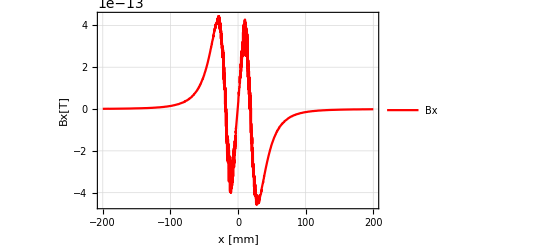
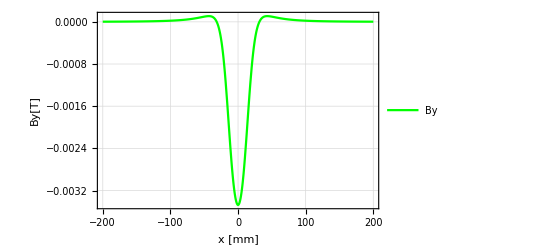
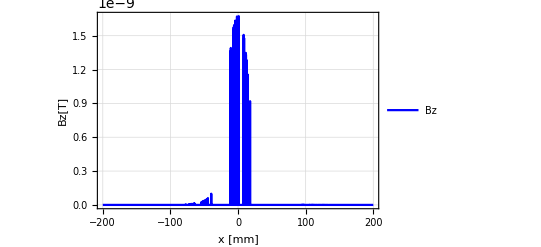

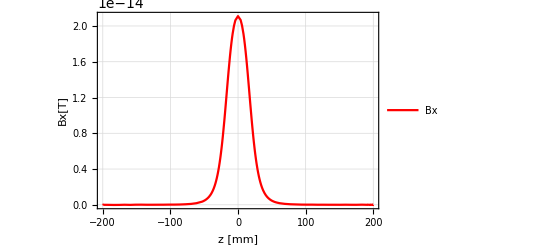
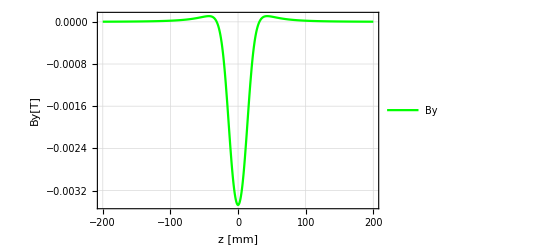
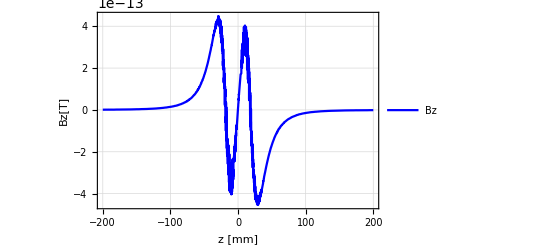

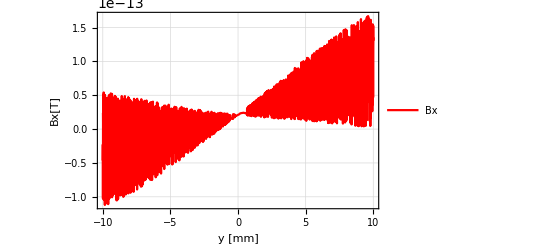
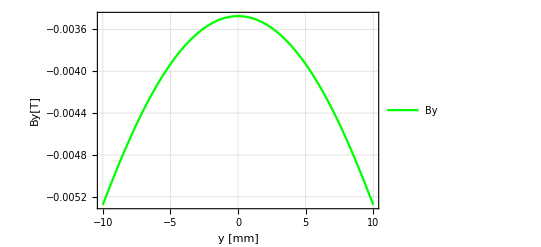

```mathematica
PlotFields[magnet, "x",{-200, 200} ]
PlotFields[magnet, "z",{-200, 200} ]
PlotFields[magnet, "y",{-10, 10} ]
```

```mathematica
FieldIntegrals[magnet, "Bx", 0, 0,{-200, 200}, 1000, 0] ;
FieldIntegrals[magnet, "By", 0, 0,{-200, 200}, 1000, 0] ;
FieldIntegrals[magnet, "Bz", 0, 0,{-200, 200}, 1000, 0] ;
```

Bx First integral: -2.7918×10^-9 G.cm

Bx Second integral: -5.58932×10^-11 kG.cm.b2

By First integral: -95.5741 G.cm

By Second integral: -1.91339 kG.cm.b2

Bz First integral: 1.5021×10^-10 G.cm

Bz Second integral: -5.5313×10^-11 kG.cm.b2

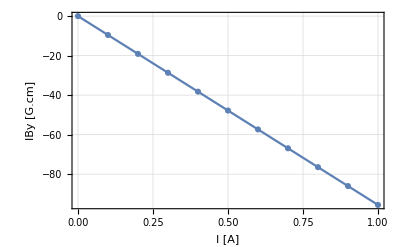

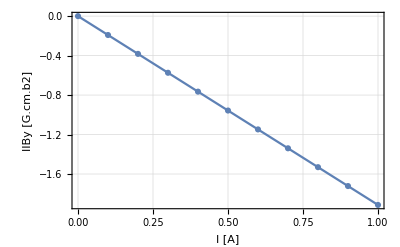

```mathematica
Currents = Range[0, 10]*0.1;
IBys = {};
IIBys = {};

For[i=1,i≤ Length[Currents],i++,
magnet =  CreateMagnetModel[Currents[[i]]]; 
{IBy, IIBy} = FieldIntegrals[magnet, "By", 0, 0,{-200, 200}, 1000, 1] ;
AppendTo[IBys, IBy];
AppendTo[IIBys, IIBy];
]

ListPlot[Transpose@{Currents, IBys}, Joined->True, PlotMarkers->Automatic, PlotTheme->"Detailed", FrameLabel->{"I [A]", "IBy [G.cm]"}]
ListPlot[Transpose@{Currents, IIBys}, Joined->True, PlotMarkers->Automatic, PlotTheme->"Detailed", FrameLabel->{"I [A]", "IIBy [G.cm.b2]"}]
```

```mathematica
line=Fit[Transpose@{Currents, IBys},{1,x},x]
parabola=Fit[Transpose@{Currents, IBys},{1,x, x^2},x]

line=Fit[Transpose@{Currents, IIBys},{1,x},x]
parabola=Fit[Transpose@{Currents, IIBys},{1,x, x^2},x]
```

1.26919×10^-8-95.5741 x

3.22759×10^-9-95.5741 x-6.30956×10^-8 x^2

2.83834×10^-10-1.91339 x

1.17555×10^-10-1.91339 x-1.10852×10^-9 x^2

```mathematica
FieldIntegralsMap["bobina_field_integrals_current=1A_Z=-200_200mm.txt", magnet,{-10, 10}, {-10, 10}, {-200, 200}, 21, 21, 1000 ];
```

Saved in file: bobina_field_integrals_current=1A_Z=-200_200mm.txt